## good hygiene

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

## first integral

### analytic

```mathematica
∫_0^∞ Exp[-p^2/2]ⅆp
```

√(π/2)

### numeric

```mathematica
NIntegrate[Exp[-p^2/2],{p,0,∞}]
```

1.25331

```mathematica
Table[
Print["integral from 0 to ",10^k," = ",NIntegrate[Exp[-p^2/2],{p,0,10^k}]]
,{k,6}];
```

integral from 0 to 10 = 1.25331

integral from 0 to 100 = 1.25331

integral from 0 to 1000 = 1.25331

integral from 0 to 10000 = 0.

integral from 0 to 100000 = 0.

integral from 0 to 1000000 = 0.

## second integral

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,dϕ=0,gϕ=0},
H=(p^2+(gϕ/as)^2)/2+m^4((1-(ϕ/M)^2)^(-1/2)-1);
Print["H = ",H];
Print["integrand = ",Exp[-at H as^3]];
Print["integral = ",∫_0^∞ Exp[-at H as^3]ⅆp];
]
```

H = p^2/2

integrand = ⅇ^(-p^2/2)

integral = √(π/2)

## third integral

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,dϕ=0,gϕ=0},
H=(p^2+(gϕ/as)^2)/2+m^4((1-(ϕ/M)^2)^(-1/2)-1);
Print["H = ",H];
Print["integrand = ",Cos[as^3 dϕ p]Exp[-at H as^3]];
Print["integral = ",∫_0^∞ Cos[as^3 dϕ p]Exp[-at H as^3]ⅆp];
]
```

H = p^2/2

integrand = ⅇ^(-p^2/2)

integral = √(π/2)

## fourth integral

H = p^2/2

Cos[as^3dϕ p] = 1

integrand = 1/2 ⅇ^(-p^2/2) p^2

integral = (√(π/2))/2

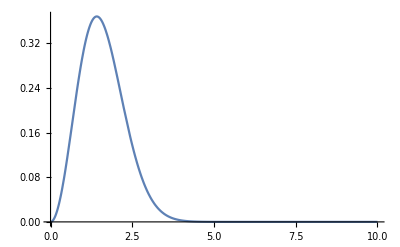

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,dϕ=0,gϕ=0},
H=(p^2+(gϕ/as)^2)/2+m^4((1-(ϕ/M)^2)^(-1/2)-1);
Print["H = ",H];
Print["Cos[as^3dϕ p] = ",Cos[as^3 dϕ p]];
Print["integrand = ",H Cos[as^3 dϕ p]Exp[-at H as^3]];
Print["integral = ",∫_0^∞ H Cos[as^3 dϕ p]Exp[-at H as^3]ⅆp];
Plot[H Cos[as^3 dϕ p]Exp[-at H as^3],{p,0,10}]
]
```

### excursion for finite dϕ

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,gϕ=0},
H=(p^2+(gϕ/as)^2)/2+m^4((1-(ϕ/M)^2)^(-1/2)-1);
Print["H = ",H];
Print["integrand = ",H Cos[as^3 dϕ p]Exp[-at H as^3]];
Print["integral = ",∫_0^∞ H Cos[as^3 dϕ p]Exp[-at H as^3]ⅆp];
]
```

H = p^2/2

integrand = 1/2 ⅇ^(-p^2/2) p^2 Cos[dϕ p]

integral = -1/2 (-1+dϕ^2) ⅇ^(-dϕ^2/2) √(π/2)

## example

H = p^2/2

Cos[as^3dϕ p] = Cos[(p π)/10]

integrand = 1/2 ⅇ^(-p^2/2) p^2 Cos[(p π)/10]

integral = -1/200 ⅇ^(-π^2/200) √(π/2) (-100+π^2)

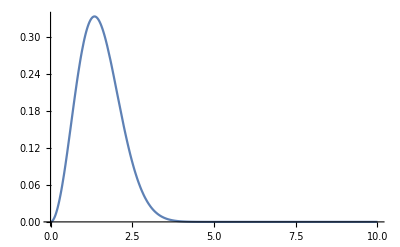

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,dϕ=π/10,gϕ=0},
H=(p^2+(gϕ/as)^2)/2+m^4((1-(ϕ/M)^2)^(-1/2)-1);
Print["H = ",H];
Print["Cos[as^3dϕ p] = ",Cos[as^3 dϕ p]];
Print["integrand = ",H Cos[as^3 dϕ p]Exp[-at H as^3]];
Print["integral = ",∫_0^∞ H Cos[as^3 dϕ p]Exp[-at H as^3]ⅆp];
Plot[H Cos[as^3 dϕ p]Exp[-at H as^3],{p,0,10}]
]
```

```mathematica
Chop[Solve[1/2 ⅇ^(-p^2/2) p^2 ==10^-20,p]//N]
```

{{p→1.41421×10^-10},{p→-1.41421×10^-10},{p→9.9963},{p→-9.9963}}

```mathematica
Block[{as=1,at=1,M=1,m=1,ϕ=0,dϕ=π/10,gϕ=0,ω=9.999},
Print["domain of integration = 0 - ",ω];
Print["analytic integral = ",Chop[∫_0^ω H Exp[-at H as^3]Cos[as^3 dϕ p]ⅆp]];
Print["numeric integral = ",NIntegrate[H Exp[-at H as^3] Cos[as^3 dϕ p],{p,0,ω}]];
]
```

domain of integration = 0 - 9.999

analytic integral = 0.537613

numeric integral = 0.537613

## save results

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```